27.9602

13.823

0.02

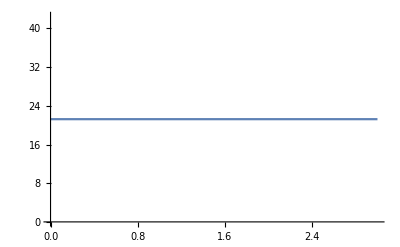

4.20973

-0.00150796

1.18305×10^-7

0.707107

2.2

10.4458

-Graphics3D-

{{W→InterpolatingFunction[{{-50., 50.}, {0., 3.}}, <>]}}

-Graphics3D-

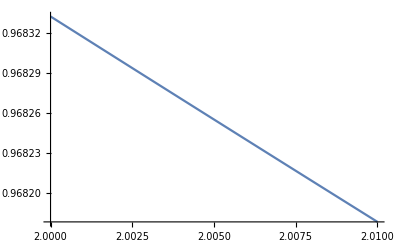

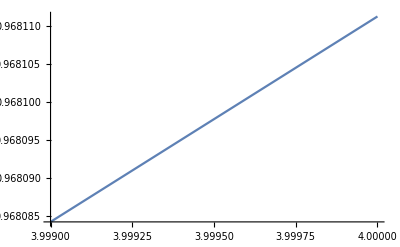

```mathematica
kappa = (2 * Pi)* (4.44 +1*0.01)
gamma =(2 * Pi) * (2.30 -1*0.1)
T = 0.02(*temperature in Kelvin*)
aalpha[t_]:=(0.51-0.4*0.004) *(kappa + gamma)
Plot[aalpha[t], {t,0,3}]
Delta =(2 * Pi)* (0.70 -0.3* 0.10)
K = -(2 * Pi)* (0.0002 + 1* 0.00004)
nT = 0.5 * Coth[ 0.319/(2T)] - 0.5
sigmaSP = Sqrt[nT + 1/2]
b=1.1Sqrt[4]
U[Q_,t_] := (2/(aalpha[t] + (kappa + gamma)/2))* (0.25*( (kappa/2 + gamma/2)^2 + Delta^2 - aalpha[t]^2)* Q^2 + (3/2)* Delta *K* Q^4 + 3 K^2 Q^6) + Sqrt[2 kappa]* b *HeavisideTheta[t-0.228]*HeavisideTheta[1.228+0.14-t]*Q
Diff = 0.5*(kappa + gamma)*(nT + 1/2)
Plot3D[U[Q,t], {Q, -15, 15}, {t,0,3}]
S=NDSolve[{D[W[Q,t],t] == D[W[Q,t],Q]*D[U[Q,t],Q] +W[Q,t]*D[U[Q,t],Q,Q]+ Diff * D[W[Q,t],Q,Q], W[Q,0] == (1/(Sqrt[2 Pi] sigmaSP)) Exp[-Q^2/(2 sigmaSP^2)], W[50,t]== 0, W[-50,t]== 0}, W, {Q,-50,50},{t,0,3}]
WW[Q_,t_] :=Evaluate[W[Q,t]/.S] 
Plot3D[WW[Q,t],{Q,-25,25},{t,0,3},PlotRange->All]
P[t_] := Integrate[WW[Q,t], {Q,-7.5,7.5}]
Pdetected[t_] := 1 - P[t]
Plot[Pdetected[t], {t,2,2.01}]
Plot[(1-Exp[-(0.703^(1/(1 + 0.12 nbar)))*nbar])*0.744 + 0.256, {nbar, 3.999, 4}, PlotRange->All]
(*Plot[{P[t]/P[1.7],Exp[-1.1(t-0.15)]}, {t,0,4}]
Plot[-Log[P[t]]/(b^2 (t-1.2)), {t,0,4}] *)
 (* note from this plot that Pdark is around 2.5 for a 1 microsec pulse, which is what is observed experimentally*)
```